-----------Fig S1-----------

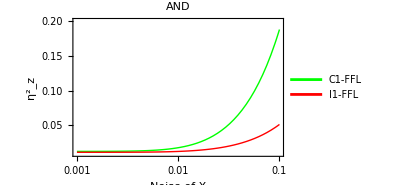
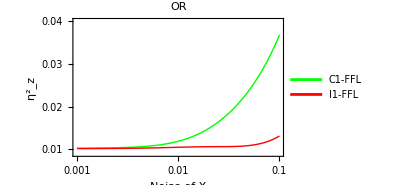
-Graphics- | -Graphics-

-----------Fig S2-----------

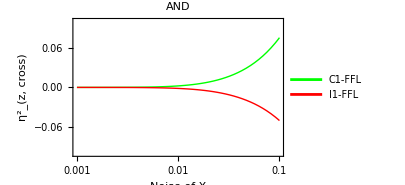
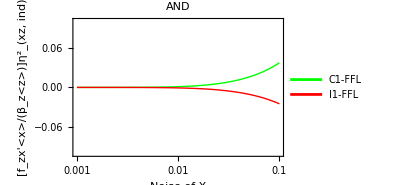
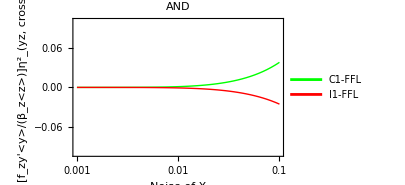
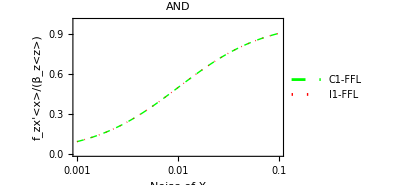
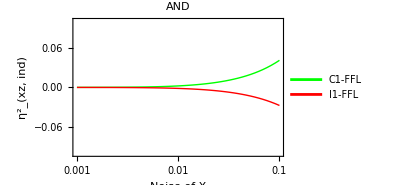
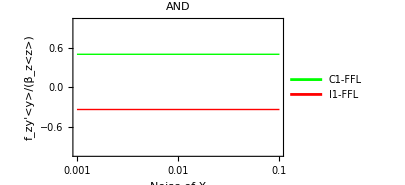
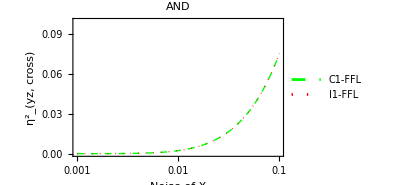
-Graphics- |  |  | 
-Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

-----------Fig S3-----------

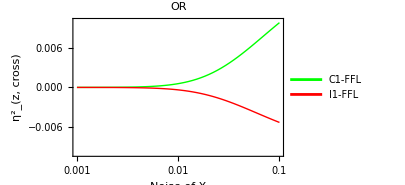
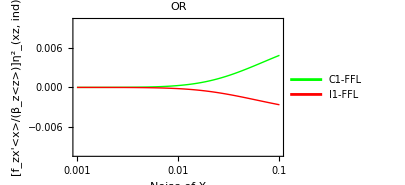
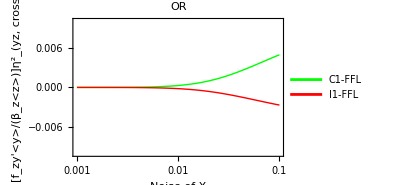
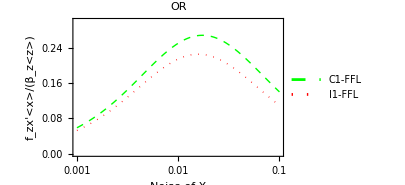
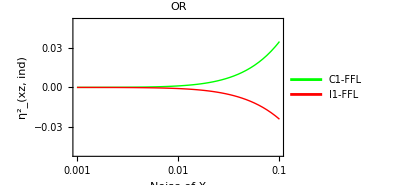
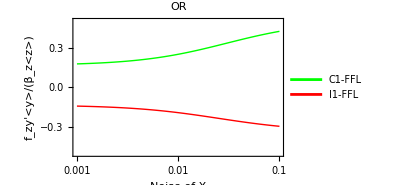
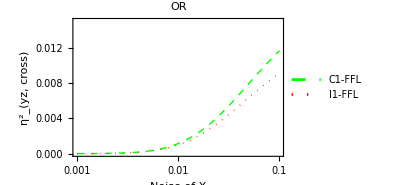
-Graphics- |  |  | 
-Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

-----------Fig 3c-----------

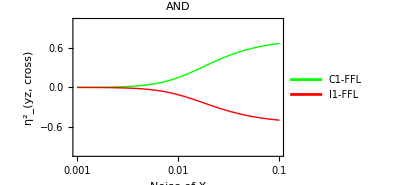

-----------Fig S4-----------

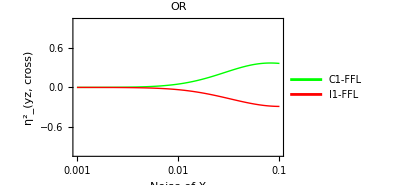

```mathematica
(*
Notations: xav=<x>, yav=<y>, zav=<z>
		fijp=Subscript[f, ij]'
*)
(*------Squared coefficient of variation: Subscript[CV^2, i]=Subscript[σ^2, i]/(<i>^2), Subscript[CV^2, ij]=Subscript[σ^2, ij]/(<i><j>)------*)

Γxy=1/(βx+βy);
Γxz=1/(βx+βz);
Γyz=1/(βy+βz);
Γxyz1=1/((βx+βy)*(βx+βz));
Γxyz2=(βx+βy+βz)/(βy*(βx+βy)*(βx+βz)*(βy+βz));
Γxyz3=(2*βx+βy+βz)/((βx+βy)*(βx+βz)*(βy+βz));



ηxy=Γxy/yav*fyxp; (*Subscript[η^2, xy]*)

ηxz1=Γxz/zav*fzxp; (*Subscript[η^2, xz,d]*)
ηxz2=Γxyz1/zav*fyxp*fzyp; (*Subscript[η^2, xz,ind]*)
ηxz=ηxz1+ηxz2; (*Subscript[η^2, xz]*)

ηyz1=Γyz/zav*fzyp; (*Subscript[η^2, yz,Subscript[ind, 1]]*)
ηyz2=(Γxyz2*xav)/(yav*zav)*fyxp^2*fzyp; (*Subscript[η^2, yz,Subscript[ind, 2]]*)
ηyz3=(Γxyz3*xav)/(yav*zav)*fyxp*fzxp; (*Subscript[η^2, yz,cross]*)
ηyz=ηyz1+ηyz2+ηyz3; (*Subscript[η^2, yz]*)



ηzi=1/zav; (*Subscript[η^2, z,int]*)

ηzd=(fzxp*xav)/(βz*zav)*ηxz1; (*Subscript[η^2, z,d]*)

ηzind=(fzyp*yav)/(βz*zav)*(ηyz1+ηyz2); (*Subscript[η^2, z,ind]*)

prefactor1=(fzxp*xav)/(βz*zav);
ηzsyn1=prefactor1*ηxz2; 
prefactor2=(fzyp*yav)/(βz*zav);
ηzsyn2=prefactor2*ηyz3; 
ηzsyn=ηzsyn1+ηzsyn2; (*Subscript[η^2, z,cross]*)

ηp=ηzi+ηzd+ηzind; (*Subscript[η^2, z,path]*)

ηz=ηp+ηzsyn; (*Subscript[η^2, z]*)

ηr=ηzsyn/ηp; (*Relative synergy noise*)


(*------Particular motifs and their functions------*)
(*C1-FFL-AND*)
Clear[Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,βx,βy,βz,xav,yav,zav];

βx=0.1; βy=1.0; βz=10.0;
yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=100;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*fzy*Kxz/(Kxz+xav)^2; fzyp=αz*fzx*Kyz/(Kyz+yav)^2;

(*Fig S1*)
ηzca=ηz; (*Subscript[η^2, z]*) 

(*Fig S2*)
ηzsca=ηzsyn; (*Subscript[η^2, z,cross]*)
ηzs1ca=ηzsyn1; 
ηzs2ca=ηzsyn2;
p1ca=prefactor1;
ηxz2ca=ηxz2;
p2ca=prefactor2;
ηyz3ca=ηyz3;

(*Fig 3c*)
ηrca=ηr;

(*I1-FFL-AND*)
Clear[Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,βx,βy,βz,xav,yav,zav];

βx=0.1; βy=1.0; βz=10.0;
yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=200;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx*fzy);
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*fzy*Kxz/(Kxz+xav)^2; fzyp=αz*fzx*-Kyz/(Kyz+yav)^2;

(*Fig S1*)
ηzia=ηz; (*Subscript[η^2, z]*) 

(*Fig S2*)
ηzsia=ηzsyn; (*Subscript[η^2, z,cross]*)
ηzs1ia=ηzsyn1; 
ηzs2ia=ηzsyn2;
p1ia=prefactor1;
ηxz2ia=ηxz2;
p2ia=prefactor2;
ηyz3ia=ηyz3;

(*Fig 3c*)
ηria=ηr;

(*C1-FFL-OR*)
Clear[Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,βx,βy,βz,xav,yav,zav];

βx=0.1; βy=1.0; βz=10.0;
yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=100;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx+fzy);
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*Kxz/(Kxz+xav)^2; fzyp=αz*Kyz/(Kyz+yav)^2;

(*Fig S1*)
ηzco=ηz; (*Subscript[η^2, z]*) 

(*Fig S3*)
ηzsco=ηzsyn; (*Subscript[η^2, z,cross]*)
ηzs1co=ηzsyn1; 
ηzs2co=ηzsyn2;
p1co=prefactor1;
ηxz2co=ηxz2;
p2co=prefactor2;
ηyz3co=ηyz3;

(*Fig S4*)
ηrco=ηr;

(*I1-FFL-OR*)
Clear[Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,βx,βy,βz,xav,yav,zav];

βx=0.1; βy=1.0; βz=10.0;
yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=200;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx+fzy);
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*Kxz/(Kxz+xav)^2; fzyp=αz*-Kyz/(Kyz+yav)^2;

(*Fig S1*)
ηzio=ηz; (*Subscript[η^2, z]*) 

(*Fig S3*)
ηzsio=ηzsyn; (*Subscript[η^2, z,cross]*)
ηzs1io=ηzsyn1; 
ηzs2io=ηzsyn2;
p1io=prefactor1;
ηxz2io=ηxz2;
p2io=prefactor2;
ηyz3io=ηyz3;

(*Fig S4*)
ηrio=ηr;
(********************************************************)

xav=1/inx; (*intx=Subscript[η^2, x]*)

inxi=0.001; inxf=0.1;

p1=LogLinearPlot[{ηzca,ηzia},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","(η^2)_z"},ImageSize->300,PlotRange->{{0.001,0.1},{0.009,0.2}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"AND"];

p2=LogLinearPlot[{ηzco,ηzio},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","(η^2)_z"},ImageSize->300,PlotRange->{{0.001,0.1},{0.009,0.04}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"OR"];

Print["-----------Fig S1-----------"];
Grid[{{p1,p2}}]


p3=LogLinearPlot[{ηzsca,ηzsia},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","(η^2)_(z, cross)"},ImageSize->300,PlotRange->{{0.001,0.1},{-0.1,0.1}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"AND"];

p4=LogLinearPlot[{ηzs1ca,ηzs1ia},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","[f_zx'<x>/(β_z<z>)](η^2)_(xz, ind)"},ImageSize->300,PlotRange->{{0.001,0.1},{-0.1,0.1}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"AND"];

p5=LogLinearPlot[{ηzs2ca,ηzs2ia},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","[f_zy'<y>/(β_z<z>)](η^2)_(yz, cross)"},ImageSize->300,PlotRange->{{0.001,0.1},{-0.1,0.1}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"AND"];

p6=LogLinearPlot[{p1ca,p1ia},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick,Dashed},{Red,Thick,Dotted}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","f_zx'<x>/(β_z<z>)"},ImageSize->300,PlotRange->{{0.001,0.1},{0.0,1.0}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"AND"];

p7=LogLinearPlot[{ηxz2ca,ηxz2ia},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","(η^2)_(xz, ind)"},ImageSize->300,PlotRange->{{0.001,0.1},{-0.1,0.1}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"AND"];

p8=LogLinearPlot[{p2ca,p2ia},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","f_zy'<y>/(β_z<z>)"},ImageSize->300,PlotRange->{{0.001,0.1},{-1.0,1}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"AND"];

p9=LogLinearPlot[{ηyz3ca,ηyz3ia},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick,Dashed},{Red,Thick,Dotted}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","(η^2)_(yz, cross)"},ImageSize->300,PlotRange->{{0.001,0.1},{0.0,0.1}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"AND"];

Print["-----------Fig S2-----------"];
Grid[{{p3},{p4,p5},{p6,p7,p8,p9}}]


p10=LogLinearPlot[{ηzsco,ηzsio},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","(η^2)_(z, cross)"},ImageSize->300,PlotRange->{{0.001,0.1},{-0.01,0.01}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"OR"];

p11=LogLinearPlot[{ηzs1co,ηzs1io},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","[f_zx'<x>/(β_z<z>)](η^2)_(xz, ind)"},ImageSize->300,PlotRange->{{0.001,0.1},{-0.01,0.01}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"OR"];

p12=LogLinearPlot[{ηzs2co,ηzs2io},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","[f_zy'<y>/(β_z<z>)](η^2)_(yz, cross)"},ImageSize->300,PlotRange->{{0.001,0.1},{-0.01,0.01}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"OR"];

p13=LogLinearPlot[{p1co,p1io},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick,Dashed},{Red,Thick,Dotted}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","f_zx'<x>/(β_z<z>)"},ImageSize->300,PlotRange->{{0.001,0.1},{0.0,0.3}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"OR"];

p14=LogLinearPlot[{ηxz2co,ηxz2io},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","(η^2)_(xz, ind)"},ImageSize->300,PlotRange->{{0.001,0.1},{-0.05,0.05}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"OR"];

p15=LogLinearPlot[{p2co,p2io},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","f_zy'<y>/(β_z<z>)"},ImageSize->300,PlotRange->{{0.001,0.1},{-0.5,0.5}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"OR"];

p16=LogLinearPlot[{ηyz3co,ηyz3io},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick,Dashed},{Red,Thick,Dotted}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","(η^2)_(yz, cross)"},ImageSize->300,PlotRange->{{0.001,0.1},{0.0,0.015}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"OR"];

Print["-----------Fig S3-----------"];
Grid[{{p10},{p11,p12},{p13,p14,p15,p16}}]


p17=LogLinearPlot[{ηrca,ηria},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","(η^2)_(yz, cross)"},ImageSize->300,PlotRange->{{0.001,0.1},{-1,1}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"AND"];

Print["-----------Fig 3c-----------"];
Grid[{{p17}}]

p18=LogLinearPlot[{ηrco,ηrio},{inx,inxi,inxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Noise of X","(η^2)_(yz, cross)"},ImageSize->300,PlotRange->{{0.001,0.1},{-1,1}},PlotLegends->{"C1-FFL","I1-FFL"},PlotLabel->"OR"];

Print["-----------Fig S4-----------"];
Grid[{{p18}}]


(*Data Extraction*)
(*
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];

(*Fig S1*)
t1=Table[{inx,ηzca,ηzia,ηzco,ηzio},{inx,inxi,inxf,0.0001}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"\n"]&/@t1];
Export["F:\\Colab\\FFL-CT\\Fig-4-5-6\\Fig4-5\\inx-c1a-i1a-c1o-i1o-etaz.dat",tp1,"FieldSeparators"->"    "];

(*Fig S2*)
t1=Table[{inx,ηzsca,ηzs1ca,ηzs2ca},{inx,inxi,inxf,0.0001}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"\n"]&/@t1];
Export["F:\\Colab\\FFL-CT\\Fig-4-5-6\\Fig4-5\\inx-zsyn-syn1-syn2-ca.dat",tp1,"FieldSeparators"->"    "];

t1=Table[{inx,p1ca,ηxz2ca,p2ca,ηyz3ca},{inx,inxi,inxf,0.0001}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"   "<>toEString[#[[4]]]<>"\n"]&/@t1];
Export["F:\\Colab\\FFL-CT\\Fig-4-5-6\\Fig4-5\\inx-p1-xz2-p2-yz3-ca.dat",tp1,"FieldSeparators"->"    "];

t1=Table[{inx,ηzsia,ηzs1ia,ηzs2ia},{inx,inxi,inxf,0.0001}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"\n"]&/@t1];
Export["F:\\Colab\\FFL-CT\\Fig-4-5-6\\Fig4-5\\inx-zsyn-syn1-syn2-ia.dat",tp1,"FieldSeparators"->"    "];

t1=Table[{inx,p1ia,ηxz2ia,p2ia,ηyz3ia},{inx,inxi,inxf,0.0001}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"   "<>toEString[#[[4]]]<>"\n"]&/@t1];
Export["F:\\Colab\\FFL-CT\\Fig-4-5-6\\Fig4-5\\inx-p1-xz2-p2-yz3-ia.dat",tp1,"FieldSeparators"->"    "];


(*Fig S3*)
t1=Table[{inx,ηzsco,ηzs1co,ηzs2co},{inx,inxi,inxf,0.0001}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"\n"]&/@t1];
Export["F:\\Colab\\FFL-CT\\Fig-4-5-6\\Fig4-5\\inx-zsyn-syn1-syn2-co.dat",tp1,"FieldSeparators"->"    "];

t1=Table[{inx,p1co,ηxz2co,p2co,ηyz3co},{inx,inxi,inxf,0.0001}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"   "<>toEString[#[[4]]]<>"\n"]&/@t1];
Export["F:\\Colab\\FFL-CT\\Fig-4-5-6\\Fig4-5\\inx-p1-xz2-p2-yz3-co.dat",tp1,"FieldSeparators"->"    "];

t1=Table[{inx,ηzsio,ηzs1io,ηzs2io},{inx,inxi,inxf,0.0001}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"\n"]&/@t1];
Export["F:\\Colab\\FFL-CT\\Fig-4-5-6\\Fig4-5\\inx-zsyn-syn1-syn2-io.dat",tp1,"FieldSeparators"->"    "];

t1=Table[{inx,p1io,ηxz2io,p2io,ηyz3io},{inx,inxi,inxf,0.0001}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"   "<>toEString[#[[4]]]<>"   "<>toEString[#[[5]]]<>"   "<>toEString[#[[4]]]<>"\n"]&/@t1];
Export["F:\\Colab\\FFL-CT\\Fig-4-5-6\\Fig4-5\\inx-p1-xz2-p2-yz3-io.dat",tp1,"FieldSeparators"->"    "];

(*Fig 3c and S4*)
t1=Table[{inx,ηrca,ηria},{inx,inxi,inxf,0.0001}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t1];
Export["F:\\Colab\\FFL-CT\\Fig-4-5-6\\Fig4-5\\inx-c1a-i1a-etar.dat",tp1,"FieldSeparators"->"    "];

t1=Table[{inx,ηrco,ηrio},{inx,inxi,inxf,0.0001}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t1];
Export["F:\\Colab\\FFL-CT\\Fig-4-5-6\\Fig4-5\\inx-c1o-i1o-etar.dat",tp1,"FieldSeparators"->"    "];
*)

Quit[];
```